```mathematica
Clear[sortPointsCC];
sortPointsCC[polyinds_,indTopts_,ptsToInds_]:=Block[{cent,ordering,polyPoints},
polyPoints=Lookup[indTopts,polyinds];
cent=Mean@polyPoints;
ordering=Ordering[ArcTan[#[[1]],#[[2]]]&@(#-cent)&/@polyPoints];
Lookup[ptsToInds,Part[polyPoints,ordering]]
]
```

```mathematica
T3candidates[vertexToCell_,indTopts_,cellToVertexG_]:=Block[{outervertindices,outercellsinds,outercells,regmem,outerverticespts},
{outervertindices,outercellsinds}=Through[{Keys,Union@*Flatten@*Values}[#]]&@Select[vertexToCell,Length[#]<3&];
outercells=Lookup[indTopts,cellToVertexG@#]&/@outercellsinds;
regmem=SignedRegionDistance@*Polygon/@outercells;
outerverticespts=Lookup[indTopts,outervertindices];
{Position[(Thread[(#[outerverticespts]<0)]&/@regmem),True],outercellsinds,outercells,outervertindices}
];
```

```mathematica
T3Transition[markers_,outercellsinds_,outercells_,outervertindices_,vertToCell_,pToI_,ItoP_,CVG_]:=Block[{ci,vi,minorcellind,vert,vertexToCell=vertToCell,numcells,majorcellind,intersectcell,ptsToInd=pToI,majorcell,cellToVertexG=CVG,
commonvertexQ,edgespartof,indTopts=ItoP,edgecoords,edgesminorcell,lines,intersects,fpos,intersectpts,newptsindices,ls},
If[markers≠{},
Do[
(*take the marker and handle cases *)
{ci,vi}=marker;
minorcellind=outercellsinds[[ci]];
vert=outervertindices[[vi]];
majorcellind=If[Head[#]===Integer,numcells=1;#,numcells=Length[#];#]&@Replace[Lookup[vertexToCell,vert],{z_Integer}:> z];
intersectcell=Lookup[ptsToInd,outercells[[ci]]];
majorcell=Lookup[cellToVertexG,majorcellind];
Print[Flatten@{majorcellind,minorcellind}];
commonvertexQ=If[numcells==1,
(Union[Flatten@Cases[Partition[majorcell,2,1,1],{OrderlessPatternSequence[vert,_]}]]∩intersectcell),
Function[(Union[Flatten@Cases[Partition[#,2,1,1],{OrderlessPatternSequence[vert,_]}]]∩intersectcell)]/@majorcell
]//(If[#≠{},First@#,{}]&)@*Flatten;
Which[
(*Case A*)
numcells==1&&commonvertexQ==={},
edgespartof =Cases[Partition[cellToVertexG[majorcellind],2,1,1],{OrderlessPatternSequence[vert,_]}];
edgecoords=Lookup[indTopts,#]&/@edgespartof;
edgesminorcell=Partition[cellToVertexG[minorcellind],2,1,1];
lines=Map[Line@Lookup[indTopts,#]&,edgesminorcell];
intersects=Map[Function[x,Map[RegionIntersection[Line[x],#]&,lines]],edgecoords];
fpos=Last@FirstPosition[intersects,_Point,{2}];
intersectpts=Cases[intersects,{__?NumberQ},{-2}];
newptsindices=Range[Max[ptsToInd]+1,Max[ptsToInd]+2];
AppendTo[indTopts,Thread[newptsindices-> intersectpts]];
KeyDropFrom[indTopts,vert];
ptsToInd=AssociationMap[Reverse,indTopts];
cellToVertexG=MapAt[sortPointsCC[Flatten[#/.Thread[vert->{newptsindices}]],indTopts,ptsToInd]&,
cellToVertexG,Key[majorcellind]];
cellToVertexG=MapAt[
Block[{y},
y=Partition[#,2,1,1];
sortPointsCC[DeleteDuplicates@Flatten@Replace[y,{x:OrderlessPatternSequence@@y[[fpos]]}:>Flatten@Insert[{x},newptsindices,2],{1}],indTopts,ptsToInd]
]&,cellToVertexG,Key[minorcellind]];
,
(*Case B*)
numcells==2&&commonvertexQ==={},
edgesminorcell=Partition[cellToVertexG[minorcellind],2,1,1];
lines=Map[Line@Lookup[indTopts,#]&,edgesminorcell];
Do[
edgespartof =Cases[Partition[cellToVertexG[majcelliter],2,1,1],{OrderlessPatternSequence[vert,_]}];
edgecoords=Lookup[indTopts,#]&/@edgespartof;
intersects=Map[Function[x,Map[RegionIntersection[Line[x],#]&,lines]],edgecoords];
fpos=Last@FirstPosition[intersects,_Point,{2}];
intersectpts=Cases[intersects,{__?NumberQ},{-2}];
Scan[(If[KeyFreeQ[ptsToInd,#],
newptsindices=Max[ptsToInd]+1;
ptsToInd[#]=newptsindices;
indTopts[newptsindices]=#])&,intersectpts];
newptsindices=Lookup[ptsToInd,intersectpts];
cellToVertexG=MapAt[sortPointsCC[Flatten[#/.Thread[vert->{newptsindices}]],indTopts,ptsToInd]&,
cellToVertexG,Key[majcelliter]]
,{majcelliter,majorcellind}
];
KeyDropFrom[indTopts,vert];
ptsToInd=AssociationMap[Reverse,indTopts];
cellToVertexG=MapAt[
Block[{y},
y=Partition[#,2,1,1];
sortPointsCC[DeleteDuplicates@Flatten@Replace[y,{x:OrderlessPatternSequence@@y[[fpos]]}:>Flatten@Insert[{x},newptsindices,2],{1}],indTopts,ptsToInd]
]&,cellToVertexG,Key[minorcellind]],
(*Case C*)
numcells==1&&commonvertexQ=!={},
edgespartof =Cases[Partition[cellToVertexG[majorcellind],2,1,1],{OrderlessPatternSequence[vert,_]}];
edgecoords=Lookup[indTopts,#]&/@edgespartof;
edgesminorcell=Partition[cellToVertexG[minorcellind],2,1,1];
lines=Map[Line@Lookup[indTopts,#]&,edgesminorcell];
intersects=Map[Function[x,Map[RegionIntersection[Line[x],#]&,lines]],edgecoords];
fpos=Last@FirstPosition[intersects,_Point,{2}];
intersectpts=First@DeleteCases[Cases[intersects,{__?NumberQ},{-2}],indTopts[commonvertexQ]];
newptsindices=Max[ptsToInd]+1;
AppendTo[indTopts,newptsindices-> intersectpts];
KeyDropFrom[indTopts,{vert,commonvertexQ}];
ptsToInd=AssociationMap[Reverse,indTopts];
cellToVertexG=MapAt[DeleteDuplicates[#/.(commonvertexQ|vert)->newptsindices]&,cellToVertexG,Key[majorcellind]];
cellToVertexG=MapAt[#/.commonvertexQ->newptsindices&,cellToVertexG,Key[minorcellind]],
(*Case D*)
numcells==2&&commonvertexQ=!={},
ls={};
edgesminorcell=Partition[cellToVertexG[minorcellind],2,1,1];
lines=Map[Line@Lookup[indTopts,#]&,edgesminorcell];
Do[
edgespartof =Cases[Partition[cellToVertexG[majcelliter],2,1,1],{OrderlessPatternSequence[vert,_]}];
edgecoords=Lookup[indTopts,#]&/@edgespartof;
intersects=Map[Function[x,Map[RegionIntersection[Line[x],#]&,lines]],edgecoords];
fpos=Last@FirstPosition[intersects,_Point,{2}];
intersectpts=DeleteCases[Cases[intersects,{__?NumberQ},{-2}],indTopts[commonvertexQ]];
If[Length[intersectpts]==2,AppendTo[ls,intersectpts]];
Scan[(If[KeyFreeQ[ptsToInd,#],
newptsindices=Max[ptsToInd]+1;
ptsToInd[#]=newptsindices;
indTopts[newptsindices]=#])&,intersectpts];
newptsindices=Lookup[ptsToInd,intersectpts];
cellToVertexG=MapAt[
sortPointsCC[DeleteDuplicates@Flatten[#/.(commonvertexQ|vert)->newptsindices],indTopts,ptsToInd]&,
cellToVertexG,Key[majcelliter]];
,
{majcelliter,majorcellind}
];
cellToVertexG=MapAt[
sortPointsCC[DeleteDuplicates@Flatten[#/.commonvertexQ->Lookup[ptsToInd,intersectpts]],indTopts,ptsToInd]&,
cellToVertexG,Key[minorcellind]];
];
KeyDropFrom[indTopts,{vert,commonvertexQ}];
ptsToInd=AssociationMap[Reverse,indTopts];
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
,{marker,markers}]
];
{indTopts,ptsToInd,vertexToCell,cellToVertexG}
];
```

## Case A

```mathematica
SeedRandom[3];
mesh=VoronoiMesh[RandomReal[1,{200,2}],{{0,1},{0,1}},ImageSize-> Medium];
```

```mathematica
pts=MeshPrimitives[mesh,0]/.Point->Sequence;
cornerpts=pts[[-4;;]];
pts=pts[[1;;-5]];
```

```mathematica
$ptsToInd=ptsToInd=AssociationThread[pts-> Range@Length@pts];
$indTopts=indTopts=AssociationMap[Reverse][ptsToInd];
```

```mathematica
cellmeshprim=MeshPrimitives[mesh,2];
cells=(MeshPrimitives[#,0]&/@cellmeshprim)/.Point->Sequence/.Thread[cornerpts->Nothing];
```

```mathematica
$cellToVertexG=cellToVertexG=AssociationThread[Range[Length@cells]->Map[ptsToInd,cells,{2}]];
$vertexToCell=vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
KeyDropFrom[cellToVertexG,{9,169,199}];
```

```mathematica
indTopts[280]={0.8936,0.7856};
indTopts[60]={0.8936,0.7856};
```

```mathematica
AppendTo[indTopts,399->{0.8936,0.7856}];
```

```mathematica
KeyDropFrom[indTopts,{280,60}];
```

```mathematica
KeyDropFrom[vertexToCell,{280,60}];
```

```mathematica
AppendTo[vertexToCell,399->127];
```

```mathematica
ptsToInd=AssociationMap[Reverse,indTopts];
```

```mathematica
cellToVertexG=Map[DeleteDuplicates,cellToVertexG/.{280->399,60->399}];
```

```mathematica
vertexToCell=Association@DeleteCases[Normal[vertexToCell/. {9|169|199->Sequence[]}],HoldPattern[_ -> {}]];
```

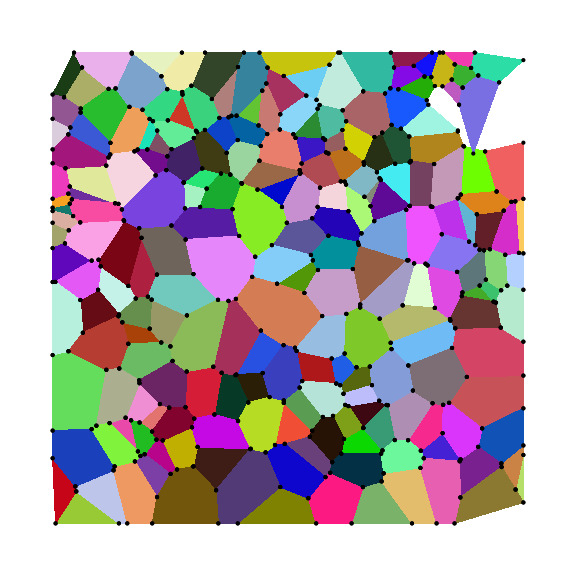

```mathematica
Graphics[{Map[{RandomColor[],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]},ImageSize->Large]
```

```mathematica
{markers,outercellsinds,outercells,outervertindices}=T3candidates[vertexToCell,indTopts,cellToVertexG];
```

```mathematica
{indTopts,ptsToInd,vertexToCell,cellToVertexG}=T3Transition[markers,outercellsinds,outercells,outervertindices,vertexToCell,ptsToInd,indTopts,cellToVertexG];
```

{127,18}

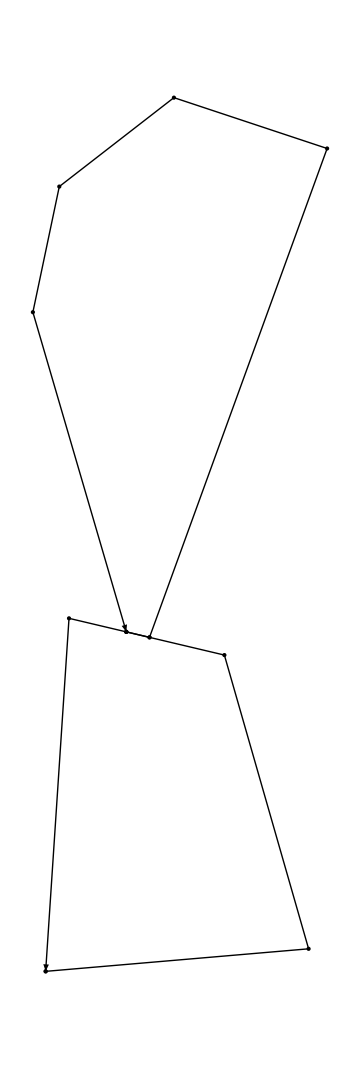

```mathematica
Graphics[Through[{Point,Arrow}[#]]&@Append[#,First@#]&@Lookup[indTopts,Lookup[cellToVertexG,#]]&/@{127,18},ImageSize->Medium]
```

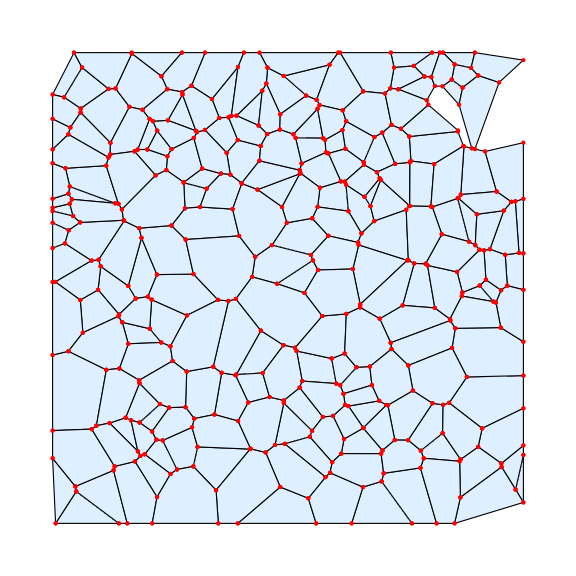

```mathematica
Graphics[{Map[{EdgeForm[Black],FaceForm[LightBlue],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],
Red,Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]//DeleteDuplicates},ImageSize->Large]
```

## Case B

```mathematica
SeedRandom[3];
mesh=VoronoiMesh[RandomReal[1,{200,2}],{{0,1},{0,1}},ImageSize-> Medium];
```

```mathematica
pts=MeshPrimitives[mesh,0]/.Point->Sequence;
cornerpts=pts[[-4;;]];
pts=pts[[1;;-5]];
```

```mathematica
$ptsToInd=ptsToInd=AssociationThread[pts-> Range@Length@pts];
$indTopts=indTopts=AssociationMap[Reverse][ptsToInd];
```

```mathematica
cellmeshprim=MeshPrimitives[mesh,2];
cells=(MeshPrimitives[#,0]&/@cellmeshprim)/.Point->Sequence/.Thread[cornerpts->Nothing];
```

```mathematica
$cellToVertexG=cellToVertexG=AssociationThread[Range[Length@cells]->Map[ptsToInd,cells,{2}]];
$vertexToCell=vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
KeyDropFrom[cellToVertexG,{9,169,199}];
```

```mathematica
indTopts[280]={0.8936,0.7856};
indTopts[60]={0.8936,0.7856};
```

```mathematica
AppendTo[indTopts,399->{0.8936,0.7856}];
```

```mathematica
KeyDropFrom[indTopts,{280,60}];
```

```mathematica
KeyDropFrom[vertexToCell,{280,60}];
```

```mathematica
AppendTo[vertexToCell,399->127];
```

```mathematica
ptsToInd=AssociationMap[Reverse,indTopts];
```

```mathematica
cellToVertexG=Map[DeleteDuplicates,cellToVertexG/.{280->399,60->399}];
```

```mathematica
vertexToCell=Association@DeleteCases[Normal[vertexToCell/. {9|169|199->Sequence[]}],HoldPattern[_ -> {}]];
```

```mathematica
cellToVertexG[127]={256,399,95,61};
```

```mathematica
AppendTo[cellToVertexG,201->{279,95,399}];
```

```mathematica
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

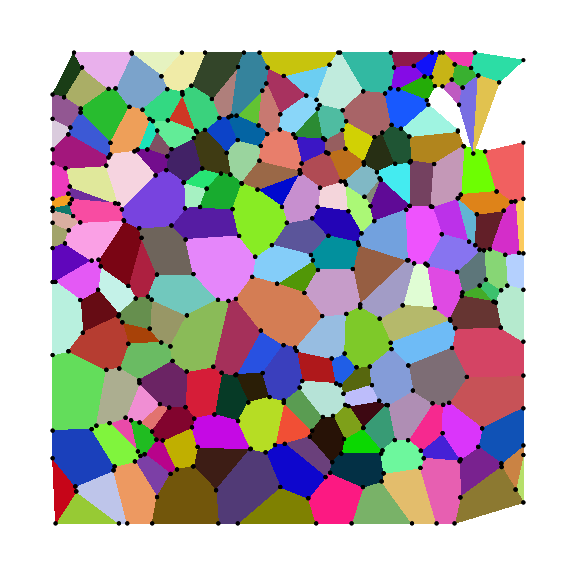

```mathematica
Graphics[{Map[{RandomColor[],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]},ImageSize->Large]
```

```mathematica
{markers,outercellsinds,outercells,outervertindices}=T3candidates[vertexToCell,indTopts,cellToVertexG];
```

```mathematica
{indTopts,ptsToInd,vertexToCell,cellToVertexG}=T3Transition[markers,outercellsinds,outercells,outervertindices,vertexToCell,ptsToInd,indTopts,cellToVertexG];
```

{127,201,18}

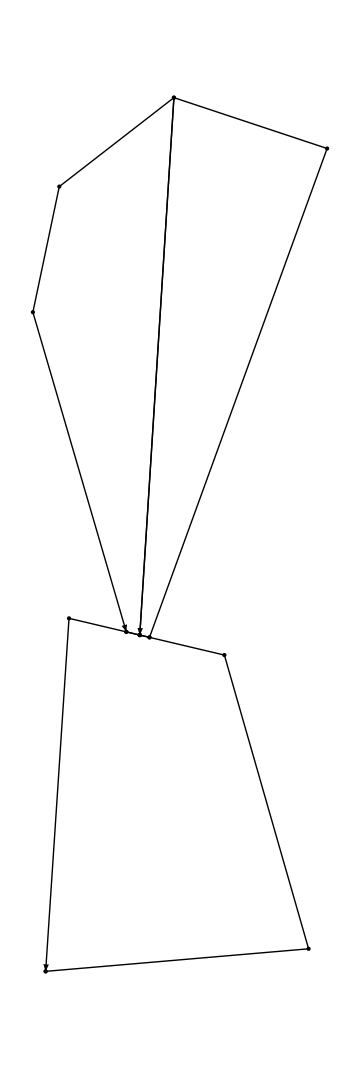

```mathematica
Graphics[Through[{Point,Arrow}[#]]&@Append[#,First@#]&@Lookup[indTopts,Lookup[cellToVertexG,#]]&/@{127,201,18},ImageSize->Medium]
```

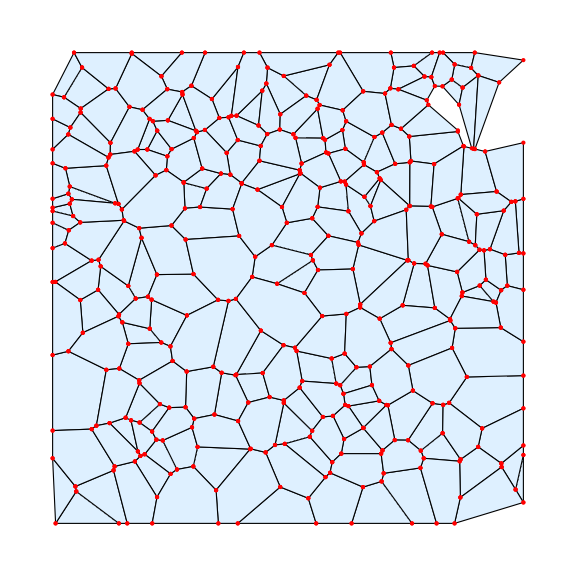

```mathematica
Graphics[{Map[{EdgeForm[Black],FaceForm[LightBlue],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],
Red,Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]//DeleteDuplicates},ImageSize->Large]
```

## Case C

```mathematica
SeedRandom[3];
mesh=VoronoiMesh[RandomReal[1,{200,2}],{{0,1},{0,1}},ImageSize-> Medium];
```

```mathematica
pts=MeshPrimitives[mesh,0]/.Point->Sequence;
```

```mathematica
cornerpts=pts[[-4;;]];
pts=pts[[1;;-5]];
```

```mathematica
$ptsToInd=ptsToInd=AssociationThread[pts-> Range@Length@pts];
$indTopts=indTopts=AssociationMap[Reverse][ptsToInd];
```

```mathematica
cellmeshprim=MeshPrimitives[mesh,2];
cells=(MeshPrimitives[#,0]&/@cellmeshprim)/.Point->Sequence/.Thread[cornerpts->Nothing];
```

```mathematica
$cellToVertexG=cellToVertexG=AssociationThread[Range[Length@cells]->Map[ptsToInd,cells,{2}]];
$vertexToCell=vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
KeyDropFrom[cellToVertexG,{9,169,199}];
```

```mathematica
vertexToCell=Association@DeleteCases[Normal[vertexToCell/. {9|169|199->Sequence[]}],HoldPattern[_ -> {}]];
```

```mathematica
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
AppendTo[indTopts,400->{1.05,0.6893896226716034}];
```

```mathematica
cellToVertexG[13]={72,331,369,400,351};
```

```mathematica
indTopts[72]={0.9828574335519906,0.6740108914858205};
```

```mathematica
indTopts[355]={1.02,0.6787049941899824};
```

```mathematica
indTopts[140]={0.997315022930967,0.7900129962646899};
```

```mathematica
ptsToInd=AssociationMap[Reverse,indTopts];
```

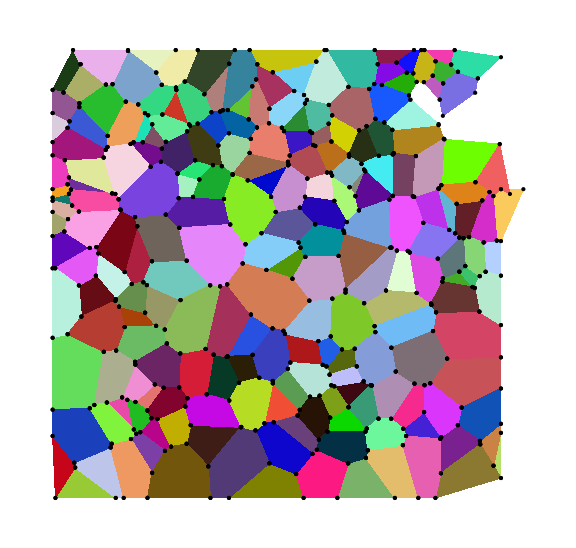

```mathematica
Graphics[{Map[{RandomColor[],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]},ImageSize->Large]
```

```mathematica
{markers,outercellsinds,outercells,outervertindices}=T3candidates[vertexToCell,indTopts,cellToVertexG];
```

```mathematica
{indTopts,ptsToInd,vertexToCell,cellToVertexG}=T3Transition[markers,outercellsinds,outercells,outervertindices,vertexToCell,ptsToInd,indTopts,cellToVertexG];
```

{97,13}

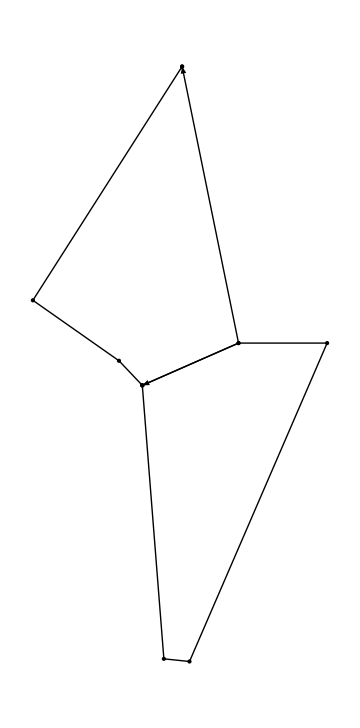

```mathematica
Graphics[Through[{Point,Arrow}[#]]&@Append[#,First@#]&@Lookup[indTopts,Lookup[cellToVertexG,#]]&/@{97,13},ImageSize->Medium]
```

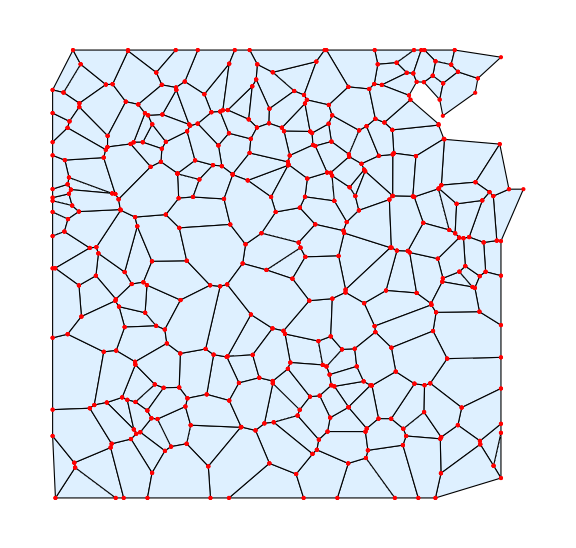

```mathematica
Graphics[{Map[{EdgeForm[Black],FaceForm[LightBlue],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],
Red,Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]//DeleteDuplicates},ImageSize->Large]
```

## Case D

```mathematica
SeedRandom[3];
mesh=VoronoiMesh[RandomReal[1,{200,2}],{{0,1},{0,1}},ImageSize-> Medium];
```

```mathematica
pts=MeshPrimitives[mesh,0]/.Point->Sequence;
```

```mathematica
cornerpts=pts[[-4;;]];
pts=pts[[1;;-5]];
```

```mathematica
$ptsToInd=ptsToInd=AssociationThread[pts-> Range@Length@pts];
$indTopts=indTopts=AssociationMap[Reverse][ptsToInd];
```

```mathematica
cellmeshprim=MeshPrimitives[mesh,2];
cells=(MeshPrimitives[#,0]&/@cellmeshprim)/.Point->Sequence/.Thread[cornerpts->Nothing];
```

```mathematica
$cellToVertexG=cellToVertexG=AssociationThread[Range[Length@cells]->Map[ptsToInd,cells,{2}]];
$vertexToCell=vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
KeyDropFrom[cellToVertexG,{9,169,199}];
```

```mathematica
vertexToCell=Association@DeleteCases[Normal[vertexToCell/. {9|169|199->Sequence[]}],HoldPattern[_ -> {}]];
```

```mathematica
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

```mathematica
AppendTo[indTopts,400->{1.05,0.6893896226716034}];
```

```mathematica
cellToVertexG[13]={72,331,369,400,351};
```

```mathematica
indTopts[72]={0.9828574335519906,0.6740108914858205};
```

```mathematica
indTopts[355]={1.02,0.6787049941899824};
```

```mathematica
indTopts[140]={0.997315022930967,0.7900129962646899};
```

```mathematica
indTopts[401]={1.05,0.7687049941899824};
```

```mathematica
ptsToInd=AssociationMap[Reverse,indTopts];
```

```mathematica
cellToVertexG[201]={140,355,401};
```

```mathematica
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

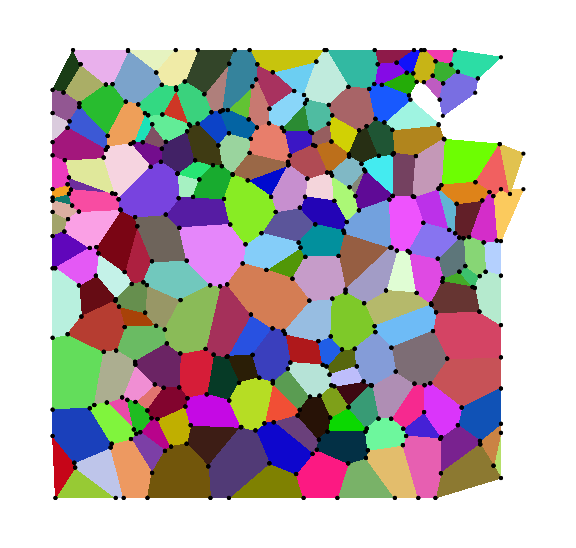

```mathematica
Graphics[{Map[{RandomColor[],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]},ImageSize->Large]
```

```mathematica
{markers,outercellsinds,outercells,outervertindices}=T3candidates[vertexToCell,indTopts,cellToVertexG];
```

```mathematica
{indTopts,ptsToInd,vertexToCell,cellToVertexG}=T3Transition[markers,outercellsinds,outercells,outervertindices,vertexToCell,ptsToInd,indTopts,cellToVertexG];
```

{97,201,13}

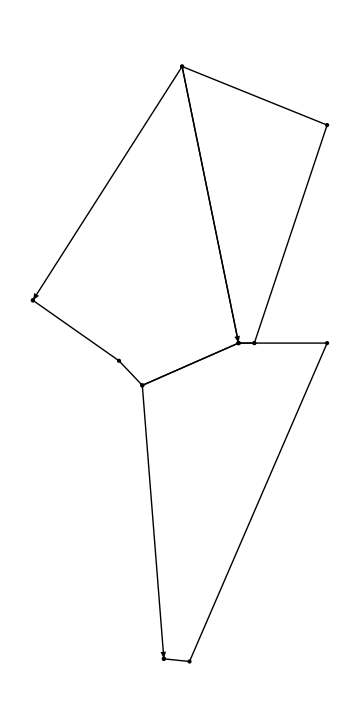

```mathematica
Graphics[Through[{Point,Arrow}[#]]&@Append[#,First@#]&@Lookup[indTopts,Lookup[cellToVertexG,#]]&/@{97,201,13},ImageSize->Medium]
```

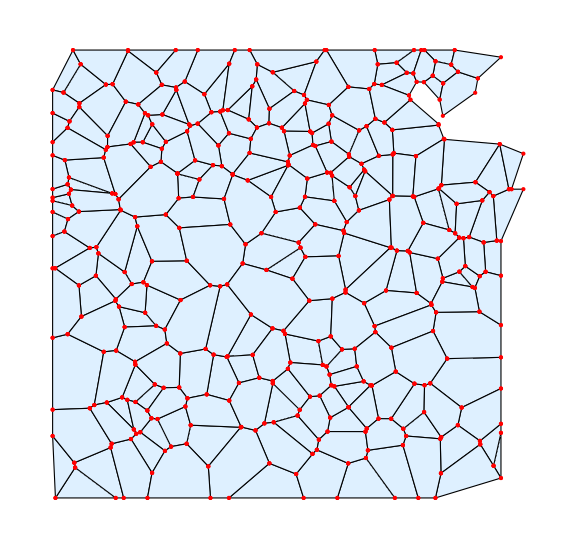

```mathematica
Graphics[{Map[{EdgeForm[Black],FaceForm[LightBlue],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],
Red,Point@Flatten[Lookup[indTopts,#]&/@Values@cellToVertexG,1]},ImageSize->Large]
```